## Sliding Mode

```mathematica
eqSlide=(1/2 ρf U^2 CD hf b)+m g Sin[θ]==μ(m g Cos[θ]-ρf g Vb-1/2 ρf U^2 CL hf b);
```

```mathematica
eqSlide1 = eqSlide/.{Vb->(m/ρp(a1((hf/Cos[θ])/hp)^2+b1((hf/Cos[θ])/hp))), b->(β hp)}//Simplify
```

hf hp^2 U^2 β (CD+CL μ) ρf Cos[θ]+(g m (2 a1 hf^2 μ ρf Sec[θ]+hp (2 b1 hf μ ρf+hp ρp Sin[2 θ])))/(hp ρp)==2 g hp m μ Cos[θ]^2

```mathematica
Solve[eqSlide1, U]//Simplify
```

{{U→-(√2 √(-g m Cos[θ]^2 (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]))},{U→(√2 √(-g m Cos[θ]^2 (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]))}}

```mathematica
Assuming[{g ∈ PositiveReals &&  hf ∈ PositiveReals &&  hb ∈ PositiveReals && ρ ∈ PositiveReals && θ∈ PositiveReals && β∈ PositiveReals && m ∈ PositiveReals }, Simplify[Solve[eqSlide1, U]]]
```

{{U→-(√2 Abs[Cos[θ]] √(-g m (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]))},{U→(√2 Abs[Cos[θ]] √(-g m (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]))}}

```mathematica
USlide1=-(√2 Abs[Cos[θ]] √(-g m (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]));
USlide2=(√2 Abs[Cos[θ]] √(-g m (b1 hf hp μ ρf Sec[θ]^2+a1 hf^2 μ ρf Sec[θ]^3+hp^2 ρp (-μ+Tan[θ]))))/(√(hf hp^3 β (CD+CL μ) ρf ρp Cos[θ]));
```

```mathematica
USlide1/.{g->9.81, m->60.0, hf->0.25, a1->0.633, b1->0.367,hp->1.70,θ->(10 Degree), μ->0.53, ρp->1050.0, ρf->1000.0 , β->0.175, CD->1.092, CL->1.197}
```

-1.69538

```mathematica
USlide2/.{g->9.81, m->60.0, hf->0.25, a1->0.633, b1->0.367,hp->1.70,θ->(10 Degree), μ->0.53, ρp->1050.0, ρf->1000.0 , β->0.175, CD->1.092, CL->1.197}
```

1.69538

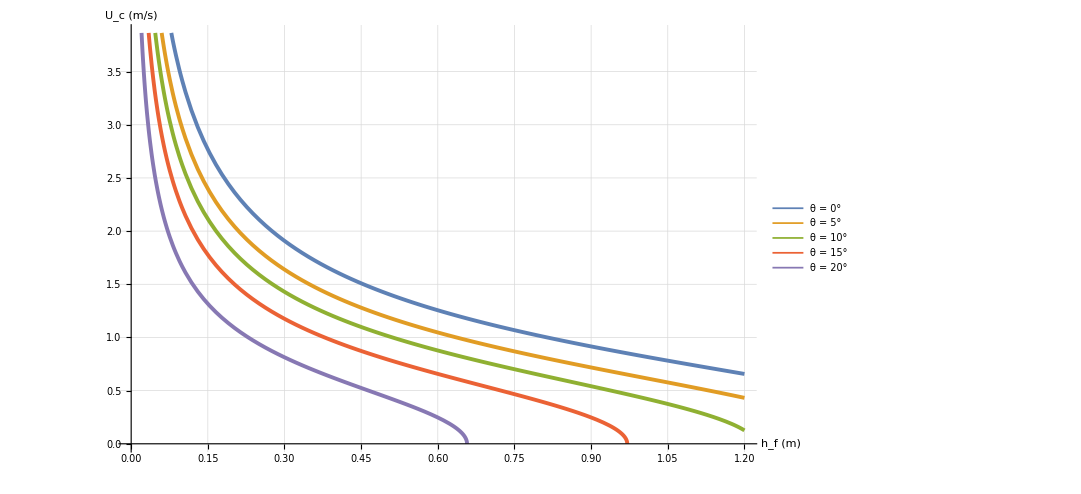

```mathematica
Plot[{USlide2/.{g->9.81, m->60.0, a1->0.62, b1->0.38,hp->1.710,θ->(0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2}, USlide2/.{g->9.81, m->60.0,  a1->0.62, b1->0.38,hp->1.710,θ->(7.0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2}, USlide2/.{g->9.81, m->60.0,  a1->0.62, b1->0.38,hp->1.710,θ->(11.50 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2},USlide2/.{g->9.81, m->60.0,  a1->0.62, b1->0.38,hp->1.710,θ->(16.0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2},USlide2/.{g->9.81, m->60.0,  a1->0.62, b1->0.38,hp->1.710,θ->(20.80 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2}}, {hf, 0.01, 1.2}, PlotStyle->{Thickness[0.0035], Thickness[0.0035],Thickness[0.0035], Thickness[0.0035],Thickness[0.0035]},PlotLegends->Placed[{Style["θ = 0°", 22.5,FontFamily->"Times"],Style["θ = 5°",22.5,FontFamily->"Times"], Style["θ = 10°",22.5,FontFamily->"Times"],Style["θ = 15°",22.5,FontFamily->"Times"], Style["θ = 20°",22.5,FontFamily->"Times"]}, {0.825, 0.76}],AxesLabel->{Style["h_f (m)",24,FontFamily->"Times"],Style["U_c (m/s)", 24,FontFamily->"Times"]}, PlotRange->{{0, Automatic},{0,Automatic}}, GridLines->Automatic, PlotPoints->100,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}},ImageSize->{800,360}]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
ucsol=Table[USlide2/.{g->9.81, m->60.0,a1->0.62, b1->0.38,hp->1.710,θ->(20.1 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, hf->xcoord[[i]]},{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\usol_20deg.txt",ucsol,"Table"]
```

Power::infy: Infinite expression 1/(√0.) encountered.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\usol_20deg.txt

## Toppling Mode

```mathematica
eqTop=(1/2 ρf U^2 CD hf b) lH+m g Sin[θ]yc==m g Cos[θ] xc -(ρf g Vb+1/2 ρf U^2 CL hf b)(1/2 hf Sin[θ]+lV)
```

1/2 b CD hf lH U^2 ρf+g m yc Sin[θ]==g m xc Cos[θ]-(1/2 b CL hf U^2 ρf+g Vb ρf) (lV+1/2 hf Sin[θ])

```mathematica
eqTop1 = eqTop//.{Vb->(m/ρp(a1((hf/Cos[θ])/hp)^2+b1((hf/Cos[θ])/hp))),lH->(1/2 hf), lV->(α  hp), xc->(hmc  Sin[θ]+lV),yc->(hmc  Cos[θ]), b->(β hp)}//Simplify
```

1/4 (CD hf^2 hp U^2 β ρf+(hf ρf (CL hp^3 U^2 β ρp+2 b1 g hp m Sec[θ]+2 a1 g hf m Sec[θ]^2) (2 hp α+hf Sin[θ]))/(hp^2 ρp)+2 g hmc m Sin[2 θ])==g m Cos[θ] (hp α+hmc Sin[θ])

```mathematica
Assuming[{g ∈ PositiveReals &&  hf ∈ PositiveReals &&  hb ∈ PositiveReals && ρ ∈ PositiveReals && θ∈ PositiveReals && α∈ PositiveReals && m ∈ PositiveReals && a1∈ PositiveReals&&b1∈ PositiveReals&& b ∈ PositiveReals}, Simplify[Solve[eqTop1, U]]]
```

{{U→-(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])))},{U→(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])))}}

```mathematica
Simplify[Solve[eqTop1, U]]
```

{{U→-(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])))},{U→(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])))}}

```mathematica
UTopSol1=-(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])));
UTopSol2=(√(g m Sec[θ]^2 (hp^2 α (-4 b1 hf ρf+3 hp ρp) Cos[θ]+hp^3 α ρp Cos[3 θ]-2 hf^2 ρf (2 a1 hp α+(a1 hf+b1 hp Cos[θ]) Sin[θ]))))/(√(hf hp^3 β ρf ρp (CD hf+2 CL hp α+CL hf Sin[θ])));
```

```mathematica
UTopSol1/.{g->9.81, m->60.0, hf->0.25, a1->0.633, b1->0.367,hp->1.70,θ->(5 Degree), μ->0.53, ρp->1050.0, ρf->1000.0 , β->0.175, CD->1.092, CL->1.197, α->0.04694}
```

-2.18064

```mathematica
UTopSol2/.{g->9.81, m->60.0, hf->0.25, a1->0.633, b1->0.367,hp->1.70,θ->(10 Degree), μ->0.53, ρp->1050.0, ρf->1000.0 , β->0.175, CD->1.092, CL->1.197, α->0.04694}
```

2.10057

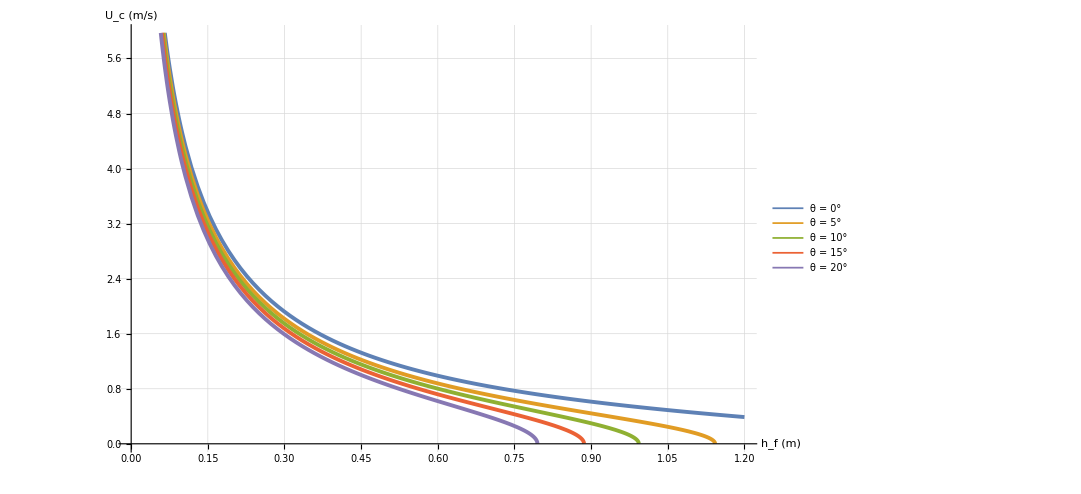

```mathematica
Plot[{UTopSol2/.{g->9.81, m->60.0, a1->0.62, b1->0.38,hp->1.710,θ->(0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694}, UTopSol2/.{g->9.81, m->60.0,  a1->0.62, b1->0.38,hp->1.710,θ->(7.0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694}, UTopSol2/.{g->9.81, m->60.0, a1->0.62, b1->0.38,hp->1.710,θ->(11.50 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694},UTopSol2/.{g->9.81, m->60.0,a1->0.62, b1->0.38,hp->1.710,θ->(16.0 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694},UTopSol2/.{g->9.81, m->60.0,a1->0.62, b1->0.38,hp->1.710,θ->(20.80 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694}}, {hf, 0.01, 1.2}, PlotStyle->{Thickness[0.0035], Thickness[0.0035],Thickness[0.0035], Thickness[0.0035],Thickness[0.0035]},PlotLegends->Placed[{Style["θ = 0°", 22.5,FontFamily->"Times"],Style["θ = 5°",22.5,FontFamily->"Times"], Style["θ = 10°",22.5,FontFamily->"Times"],Style["θ = 15°",22.5,FontFamily->"Times"], Style["θ = 20°",22.5,FontFamily->"Times"]}, {0.825, 0.76}],AxesLabel->{Style["h_f (m)",24,FontFamily->"Times"],Style["U_c (m/s)", 24,FontFamily->"Times"]}, PlotRange->{{0, Automatic},{0,Automatic}}, GridLines->Automatic, PlotPoints->100,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}},ImageSize->{800,360}]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
UTopSol2=Table[USlide2/.{g->9.81, m->60.0, a1->0.62, b1->0.38,hp->1.710,θ->(20.25 Degree), μ->0.525, ρp->1010.0, ρf->1000.0 , β->0.175, CD->1.1, CL->1.2, α->0.04694, hf->xcoord[[i]]},{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\toppling\\ucSol_20Deg.txt",UTopSol2,"Table"]
```

Power::infy: Infinite expression 1/(√0.) encountered.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\toppling\ucSol_20Deg.txt